Más formas de visualización

Se ha visto ya cómo graficar listas de datos mediante ListPlot y ListLinePlot. Si se quiere graficar varios conjuntos de datos simultáneamente, basta con indicarlos dentro de una lista.

Grafique dos conjuntos de datos simultáneamente:

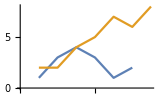

```mathematica
ListLinePlot[{{1,3,4,3,1,2},{2,2,4,5,7,6,8}}]
```

La opción PlotStyle permite especificar los estilos para cada uno de los conjuntos de datos:

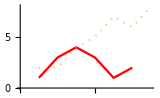

```mathematica
ListLinePlot[{{1,3,4,3,1,2},{2,2,4,5,7,6,8}},PlotStyle->{Red,Dotted}]
```

La opción Mesh permite mostrar también los puntos originales, además de las líneas:

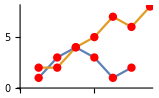

```mathematica
ListLinePlot[{{1,3,4,3,1,2},{2,2,4,5,7,6,8}},Mesh->All,MeshStyle->Red]
```

Además de observar la sucesión de los datos de una lista, muchas veces se desea ver las frecuencias con que aparece cada uno de los diferentes valores. Esto se logra con Histogram.

Aquí se muestran las longitudes de las primeras 30 palabras más comunes en inglés:

```mathematica
StringLength[Take[WordList[ ],30]]
```

{1,3,8,5,6,5,7,7,9,11,5,9,5,7,9,5,9,8,4,6,5,5,10,11,12,8,10,7,9,6}

El histograma muestra la frecuencia con que aparece cada longitud de palabra entre las primeras 200:

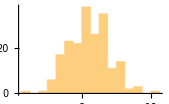

```mathematica
Histogram[StringLength[Take[WordList[ ],200]]]
```

Se obtiene un resultado más suavizado si se incluyen todas las palabras:

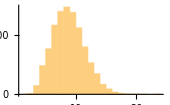

```mathematica
Histogram[StringLength[WordList[ ]]]
```

En ocasiones se tienen datos que se quieren visualizar en 3D. Por ejemplo, con GeoElevationData se puede obtener un arreglo con valores de elevación. ListPlot3D produce un gráfico 3D.

Obtenga un arreglo con valores de elevación alrededor del Monte Everest, y muéstrelos en 3 dimensiones:

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[ LinguisticAssistant  ,LinguisticAssistant]]]
```

-Graphics3D-

Muéstrelos sin la malla:

```mathematica
ListPlot3D[GeoElevationData[GeoDisk[ LinguisticAssistant  ,LinguisticAssistant]],MeshStyle->None]
```

-Graphics3D-

Una visualización alternativa es un gráfico de contornos, donde el punto de vista está colocado verticalmente arriba del objeto, y se observan las curvas de contorno correspondientes a alturas igualmente espaciadas.

Produzca un gráfico de contornos, donde los valores consecutivos de las alturas estén separados por curvas de contorno:

```mathematica
ListContourPlot[GeoElevationData[GeoDisk[ LinguisticAssistant  ,LinguisticAssistant]]]
```

-Graphics-

Cuando se tienen volúmenes muy grandes de datos, a veces es mejor usar una visualización más simple, tal como un gráfico de relieve que, en esencia, lo que hace es colorear de acuerdo con las alturas.

Genere un gráfico de relieve de la topografía dentro de 100 millas alrededor del Monte Everest:

```mathematica
ReliefPlot[GeoElevationData[GeoDisk[ LinguisticAssistant  ,LinguisticAssistant]]]
```

-Graphics-

Vocabulario

ListLinePlot[{list_1,list_2,...}] |   | grafica conjuntamente varias listas
Histogram[list] |   | obtiene un histograma
ListPlot3D[array] |   | grafica un arreglo de valores en 3D
ListContourPlot[array] |   | grafica los contornos para un arreglo de alturas
ReliefPlot[array] |   | produce un gráfico en relieve
GeoElevationData[region] |   | arreglo con elevaciones geográficas para una región
PlotStyle |   | opción para dar estilo a cada conjunto de datos
Mesh |   | si se debe incluir una malla de puntos o líneas
MeshStyle |   | opción para dar estilo a una malla

"11 Exercises Available"
"with 1 extras" | "Get Started »"

Produzca un gráfico con puntos unidos de los cuadrados, los cubos y las cuartas potencias de los enteros hasta el 10. »

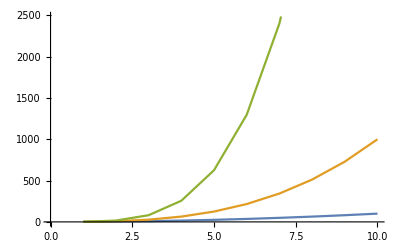
| Expected output: |  
  | -Graphics- |

Obtenga un gráfico de los 20 primeros primos, unidos con una línea, con relleno desde el eje y con un punto rojo en cada número primo. »

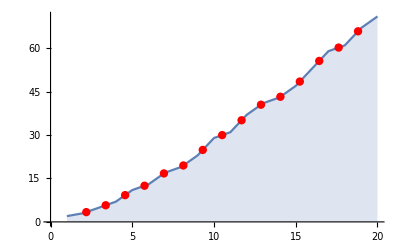
| Expected output: |  
  | -Graphics- |

Haga un gráfico en 3D de la topografía de 20 millas alrededor del Monte Fuji. »

| Expected output: |  
  | -Graphics3D- |

Genere un gráfico en relieve de la topografía de 100 millas alrededor del Monte Fuji. »

| Expected output: |  
  | -Graphics- |

Produzca un gráfico 3D de las alturas generadas por Mod[i,j] donde i y j varían hasta el 100. »

| Expected output: |  
  | -Graphics3D- |

Forme un histograma de las diferencias entre primos consecutivos para los 10 000 primeros primos. »

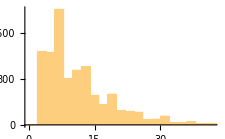
| Expected output: |  
  | -Graphics- |

Produzca un histograma de los primeros dígitos de los cuadrados de los enteros hasta el 10 000 (esto ilustra la ley de Benford). »

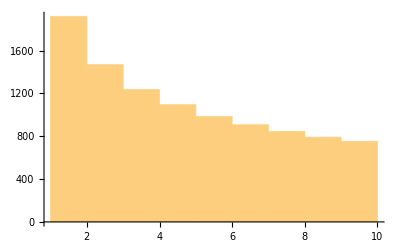
| Expected output: |  
  | -Graphics- |

Obtenga un histograma de las longitudes de los números romanos hasta el 1 000. »

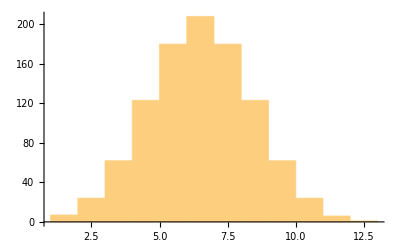
| Expected output: |  
  | -Graphics- |

Produzca un histograma de las longitudes de las oraciones en el artículo de Wikipedia sobre computadoras. »

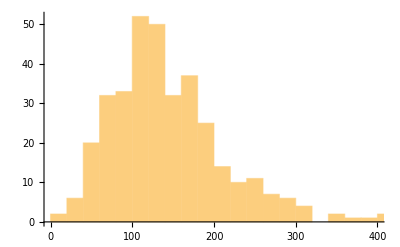
| Expected output: |  
  | -Graphics- |

Haga una lista de histogramas de 10 000 ejemplos de los totales de n reales aleatorios hasta el 100, variando n del 1 al 5 (para ilustrar el teorema central de límite). »

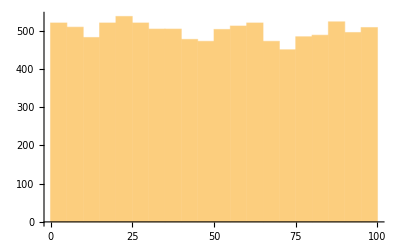
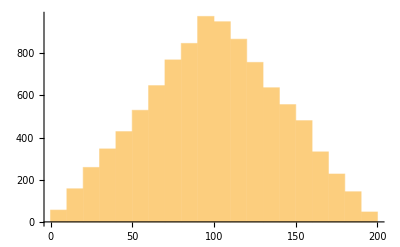
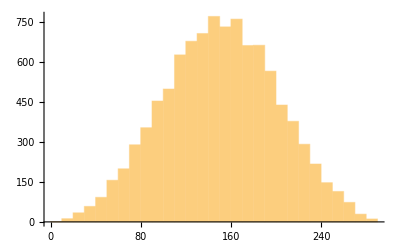
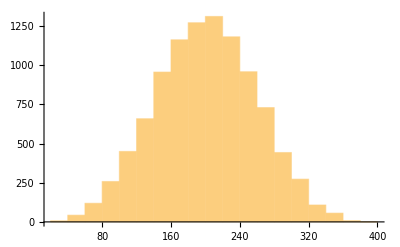
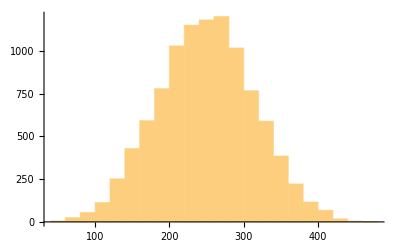
| Sample expected output: |  
  | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-} |

Genere un gráfico 3D, usando como alturas los datos de la imagen de una letra “W” binarizada, de tamaño 200. »

| Expected output: |  
  | -Graphics3D- |

Genere un histograma de las longitudes de las palabras en el artículo de Wikipedia sobre computadoras. »

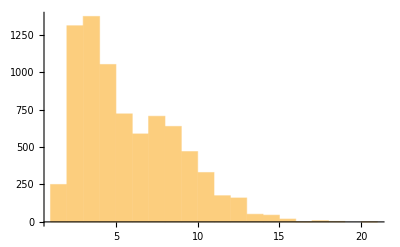
| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Qué otros tipos de visualizaciones hay?

Hay muchos, tales como ListStepPlot y ListStreamPlot, o BubbleChart y BarChart3D, o SmoothHistogram y BoxWhiskerChart, o AngularGauge y VerticalGauge.

¿Cómo se combinan los gráficos que se hayan generado separadamente?

Use Show para combinarlos sobre ejes comunes. Use GraphicsGrid, etc. (ver la Sección 37) para verlos uno tras otro.

¿Cómo se especifican los intervalos de clase en un histograma?

Histogram[list,n] usa n intervalos de clase. Histogram[list,{xmin,xmax,dx}] determina los intervalos de clase desde xmin hasta xmax en incrementos de tamaño dx.

¿Cuál es la diferencia entre un diagrama de barras y un histograma?

El diagrama de barras es una representación directa de los datos, mientras que el histograma representa la frecuencia con que ocurren los datos. En el diagrama de barras la altura de cada barra corresponde a un valor de los datos, mientras que en el histograma la altura de cada barra es el número total de valores que están dentro del tramo de valores x correspondiente a dicha barra.

¿Cómo se pueden dibujar las curvas de contorno en un gráfico topográfico en 3D?

Use las MeshFunctions→(#3&). La (#3&) es una función pura (ver la Sección 26) que utiliza la tercera coordenada (z) para hacer una malla.

¿Cómo se ponen etiquetas en un gráfico de contornos?

Use ContourLabels→All.

Notas técnicas

Wolfram Language hace muchas elecciones automáticamente en las funciones de visualización. Estas elecciones pueden pasarse por alto mediante el uso de opciones.

Una forma alternativa al uso de PlotStyle consiste en insertar Style directamente en los datos que se le dan a las funciones tales como ListLinePlot.

En una gran parte del globo terrestre, GeoElevationData contiene mediciones con una resolución de hasta unos 40 metros.

Para explorar más

Guía para la visualización de datos en Wolfram Language »